```mathematica
yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-0.5)*(mLst[[ii]]-0.5)+(x2-0.5)*(aLst[[ii]]))];
fD[gg_,ii_]:=Exp[gg*((yLst[[ii]]-mLst[[ii]]*aLst[[ii]])^2-0.5)];
matJump=Transpose[({{-(fH[h,1]*(2+fD[g,1])), fH[h,1], fH[h,1], 0, fH[h,1]*fD[g,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*(2+fD[g,2])), 0, fH[h,2], 0, fH[h,2]*fD[g,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*(2+fD[g,3])), fH[h,3], 0, 0, fH[h,3]*fD[g,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*(2+fD[g,4])), 0, 0, 0, fH[h,4]*fD[g,4]}, {fH[h,5]*fD[g,5], 0, 0, 0, -(fH[h,5]*(2+fD[g,5])), fH[h,5], fH[h,5], 0}, {0, fH[h,6]*fD[g,6], 0, 0, fH[h,6], -(fH[h,6]*(2+fD[g,6])), 0, fH[h,6]}, {0, 0, fH[h,7]*fD[g,7], 0, fH[h,7], 0, -(fH[h,7]*(2+fD[g,7])), fH[h,7]}, {0, 0, 0, fH[h,8]*fD[g,8], 0, fH[h,8], fH[h,8], -(fH[h,8]*(2+fD[g,8]))}})];
```

```mathematica
initstate=6;


matJumpBefore=N[matJump/.{g->15,h->6,x1->0,x2->0}];
matJumpR=N[matJump/.{g->15,h->6,x1->1,x2->0}];

eigenVa=Eigenvalues[matJumpR];
eigenVeR=Eigenvectors[matJumpR];
eigenVeL=Eigenvectors[Transpose[matJumpR]];
eigenVeL=Table[eigenVeL[[i]]/(eigenVeL[[i]].eigenVeR[[i]]),{i,1,8}];
(*Transpose[eigenVeL].eigenVeR*) (*verify the orthogonality of left- and right-eigenvectors*)

(*Stationary distribution*)
fWTilde[ww_]:=Join[ww[[1;;Dimensions[ww][[1]]-1]],{Table[1,Dimensions[ww][[2]]]}];

nessDist=Dot[Inverse[fWTilde[matJumpBefore]],Transpose[Table[0,Dimensions[fWTilde[matJumpBefore]][[2]]-1]~Join~{1}]];


(*Labels of the states*)
xL={1,2,3,4,1,2,3,4};
yL={1,1,1,1,2,2,2,2};

(*Propogator*)
tProp[j_,i_,t_,t0_]:=Sum[Exp[eigenVa[[m]]*(t-t0)]*eigenVeR[[m,j]]*eigenVeL[[m,i]],{m,1,8}];
(*Sum[Exp[seigenVa[[i]]*tt]*seigenVeR[[i,ii]]*nseigenVeL[[i,jj]],{i,1,8}];*)

(*Definitions of correlation*)
fEX[t_,inis_]:=Sum[xL[[i]]*tProp[i,inis,t,0],{i,1,8}];
fEY[t_,inis_]:=Sum[yL[[i]]*tProp[i,inis,t,0],{i,1,8}];
fEXY[tau_,t_,inis_]:=Sum[xL[[i]]*yL[[j]]*tProp[i,inis,t,0]*tProp[j,i,t+tau,t],{i,1,8},{j,1,8}];
fEYX[tau_,t_,inis_]:=Sum[yL[[i]]*xL[[j]]*tProp[i,inis,t,0]*tProp[j,i,t-tau,t],{i,1,8},{j,1,8}];(*\tau negative*)
fCtauP[tau_,t_,inis_]:=(fEXY[tau,t,inis]-fEX[t,inis]*fEY[t+tau,inis]);
fCtauN[tau_,t_,inis_]:=(fEYX[tau,t,inis]-fEY[t,inis]*fEX[t-tau,inis]);
(*In a generalized sense: Y affects X afterwards; \tau negative*)
fCtau[tau_,t_,inis_]:=Piecewise[{{fCtauN[tau,t,inis],tau<0},{fCtauP[tau,t,inis],tau>=0}}];
fDCtau[tau_,t_,inis_]:=fCtauP[tau,t,inis]-fCtauN[-tau,t,inis];
fPCtau[tau_,t_,inis_]:=fCtauP[tau,t,inis]+fCtauN[-tau,t,inis];
fAsym[t_,inis_]:=NIntegrate[fDCtau[tau,t,inis]/fPCtau[tau,t,inis],{tau,0,20},PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
(*stationary switch version functions*)
fsDist[t_,dist_]:=Table[Sum[tProp[i,j,t,0]*nessDist[[j]],{j,1,8}],{i,1,8}];
fsEX[t_,dist_]:=Sum[xL[[i]]*fsDist[t,dist][[i]],{i,1,8}];
fsEY[t_,dist_]:=Sum[yL[[i]]*fsDist[t,dist][[i]],{i,1,8}];
fsEXY[tau_,t_,dist_]:=Sum[xL[[i]]*yL[[j]]*fsDist[t,dist][[i]]*tProp[j,i,t+tau,t],{i,1,8},{j,1,8}];
fsEYX[tau_,t_,dist_]:=Sum[yL[[i]]*xL[[j]]*fsDist[t,dist][[i]]*tProp[j,i,t-tau,t],{i,1,8},{j,1,8}];(*\tau negative*)
fsCtauP[tau_,t_,dist_]:=(fsEXY[tau,t,dist]-fsEX[t,dist]*fsEY[t+tau,dist]);
fsCtauN[tau_,t_,dist_]:=(fsEYX[tau,t,dist]-fsEY[t,dist]*fsEX[t-tau,dist]);(*In a generalized sense: Y affects X afterwards; \tau negative*)
fsCtau[tau_,t_,dist_]:=Piecewise[{{fsCtauN[tau,t,dist],tau<0},{fsCtauP[tau,t,dist],tau>=0}}];
fsDCtau[tau_,t_,dist_]:=fsCtauP[tau,t,dist]-fsCtauN[-tau,t,dist];
fsPCtau[tau_,t_,dist_]:=fsCtauP[tau,t,dist]+fsCtauN[-tau,t,dist];
fsAsym[t_,dist_]:=NIntegrate[fsDCtau[tau,t,dist]/fsPCtau[tau,t,dist],{tau,0,20},PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
(*Above are system configurations*)
(*Below are work spaces*)
```

General::munfl: Exp[-3182.77] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {5.07781}. NIntegrate obtained 0.365973 and 2.59937 for the integral and error estimates.

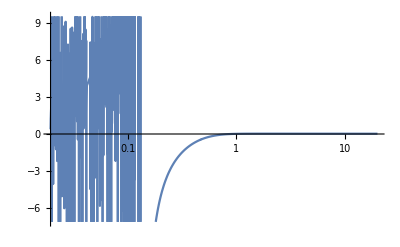

```mathematica
(*Correlation asymmetry, from a stationary distribution*)
LogLinearPlot[fsAsym[t,nessDist],{t,0,20},PlotRange->Automatic]
```

General::munfl: Exp[-3182.77] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.80438}. NIntegrate obtained 4.5567 and 0.567432 for the integral and error estimates.

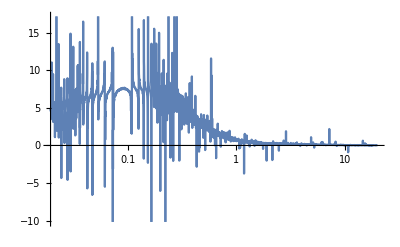

```mathematica
(*Correlation asymmetry, from a certain initial state*)
LogLinearPlot[fAsym[t,initstate],{t,0,20},PlotRange->Automatic]
```

```mathematica
isample={0,0.02,0.04,0.06,0.08,0.1,0.2,0.3,0.4,0.5,0.6,1,3,5,7,9,11,16,21,26};
```

```mathematica
asymmetryRec=Table[fAsym[i,initstate],{i,isample}]
Export["F:\\ThesisProject\\RESULTS\\09092023_asymmetry\\g15h7tau20_00_1.dat",asymmetryRec]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {6.28875}. NIntegrate obtained -0.972905 and 2.75888 for the integral and error estimates.

General::munfl: Exp[-3258.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.57}. NIntegrate obtained 1.70087 and 0.127852 for the integral and error estimates.

General::munfl: Exp[-6517.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.57}. NIntegrate obtained 1.30109 and 0.00305982 for the integral and error estimates.

General::munfl: Exp[-9776.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.57}. NIntegrate obtained 1.10522 and 0.0669076 for the integral and error estimates.

General::munfl: Exp[-13034.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.16191×10^-295 6.56058×10^-19 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13034.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.53094}. NIntegrate obtained 1.045 and 0.0696454 for the integral and error estimates.

General::munfl: Exp[-16293.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811.205] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811.204] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.53094}. NIntegrate obtained 1.05391 and 0.0279773 for the integral and error estimates.

General::munfl: Exp[-32587.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1622.41] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.49188}. NIntegrate obtained 0.928527 and 0.032617 for the integral and error estimates.

General::munfl: Exp[-48880.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2433.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.45281}. NIntegrate obtained 0.924723 and 0.08481 for the integral and error estimates.

General::munfl: Exp[-65174.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3244.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.41375}. NIntegrate obtained 0.736444 and 0.0425055 for the integral and error estimates.

General::munfl: Exp[-81467.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4056.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.41375}. NIntegrate obtained 1.00708 and 0.323923 for the integral and error estimates.

General::munfl: Exp[-97760.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4867.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.37469}. NIntegrate obtained 0.613833 and 0.0278478 for the integral and error estimates.

General::munfl: Exp[-162935.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8112.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8112.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.29656}. NIntegrate obtained 0.397407 and 0.0406365 for the integral and error estimates.

General::munfl: Exp[-488805.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24336.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.06219}. NIntegrate obtained 0.161497 and 0.0068517 for the integral and error estimates.

General::munfl: Exp[-814674.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-40560.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.945}. NIntegrate obtained 0.0984867 and 0.00388947 for the integral and error estimates.

General::munfl: Exp[-1.14054×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-56784.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.90594}. NIntegrate obtained 0.0695824 and 0.0026984 for the integral and error estimates.

General::munfl: Exp[-1.46641×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-73008.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.82781}. NIntegrate obtained 0.0562341 and 0.00200405 for the integral and error estimates.

General::munfl: Exp[-1.79228×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-89232.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.78875}. NIntegrate obtained 0.0400943 and 0.00606487 for the integral and error estimates.

General::munfl: Exp[-2.60696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-129793.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.71063}. NIntegrate obtained 0.0313674 and 0.00135724 for the integral and error estimates.

General::munfl: Exp[-3.42163×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-170353.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.67156}. NIntegrate obtained 0.0507333 and 0.0256887 for the integral and error estimates.

General::munfl: Exp[-4.23631×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-210913.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.6325}. NIntegrate obtained 0.0261673 and 0.0055207 for the integral and error estimates.

{-0.972905,1.70087,1.30109,1.10522,1.045,1.05391,0.928527,0.924723,0.736444,1.00708,0.613833,0.397407,0.161497,0.0984867,0.0695824,0.0562341,0.0400943,0.0313674,0.0507333,0.0261673}

F:\ThesisProject\RESULTS\09092023_asymmetry\g15h7tau20_00_1.dat

```mathematica
tsample={0.02,0.04,0.06,0.08,0.1,0.2};
Rasterize[Plot[Evaluate[Table[fCtau[tau,t,initstate],{t,tsample}]],{tau,-1,1},PlotRange->All,PlotLegends->Table[i,{i,tsample}]]]
(*
Export["F:\\ThesisProject\\RESULTS\\21082023_corr_proc\\x1_1x2_1\\g60h7_6_neq.pdf",%]
*)
samplingpoints=Table[Table[fCtau[tau,t,initstate],{tau,-2,2,0.01}],{t,tsample}];
skews=Table[Skewness[samplingpoints[[i]]],{i,1,Length[tsample]}]
(*
Export["F:\\ThesisProject\\RESULTS\\21082023_corr_proc\\x1_1x2_1\\g60h7_kurtosis_6_neq.dat",skews,"Table"]
*)
```

General::munfl: Exp[-3258.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

General::munfl: Exp[-3258.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-325870.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16224.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{16.369,12.1717,9.40304,7.68838,6.5838,4.45863}

```mathematica
Table[NIntegrate[fDCtau[tau,t,initstate],{tau,0,5}]/NIntegrate[fPCtau[tau,t,initstate],{tau,0,5}],{t,40,100,10}]
```

General::munfl: Exp[-2.45986×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.42812×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.229848,-0.232931,-0.233535,-0.233621,-0.233438,-0.232155,-0.22419}